```mathematica
list = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

20

200

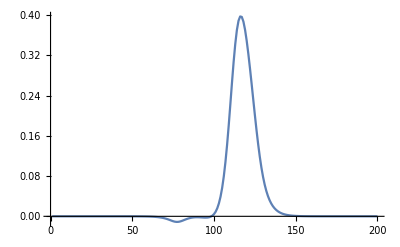

```mathematica
ListLinePlot[-list[[6]],PlotRange->All]
```

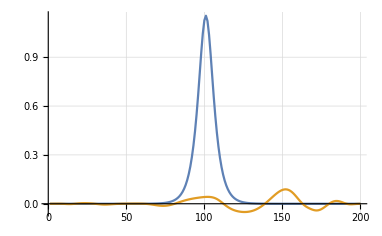

```mathematica
c1=-list[[1]][[1]];
c2=-list[[1]][[1]];
ListLinePlot[{-list[[1]]-c,-list[[-1]]-c},PlotRange->Full,GridLines->Automatic]
```

```mathematica
f1=NIntegrate[Interpolation[list[[1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[list[[-1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

27.1576

27.1581

0.0000190716

```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
list2 = Import[NotebookDirectory[]<>"/res/out_3.0.txt","Table"];
max=Max[Max[Map[Max,-list1]],Max[Map[Max,-list2]]];
min=Min[Min[Map[Min,-list1]],Min[Map[Min,-list2]]];
```

```mathematica
Manipulate[
l1=-list1[[n]] + list1[[n,1]];
l2=-list2[[n]] + list2[[n,1]];
ListLinePlot[{l1,l2},PlotRange->{min,max}],
{n,1,Length[list2],1}]
```

Part::partd: Part specification list1⟦16⟧ is longer than depth of object.

Part::partd: Part specification list1⟦16,1⟧ is longer than depth of object.

Part::partd: Part specification list2⟦16⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$19191::prng: Value of option PlotRange -> {min,max} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.